# Digital Logic in Stochastic CRNs

This notebook was prepared by Erik Winfree <winfree@caltech.edu> for Caltech BE/CS 191a, Winter 2022.  
Do not share this with anyone who is not currently taking the class unless you have permission from Erik Winfree.

## Stochastic CRN simulator preliminaries

We load the SSA simulator and borrow some useful functions from StochasticCRNsInFiniteVolumes.nb.  We have also augmented the functionality of PlotFormat to make it convenient to plot expressions involving species counts (with examples in the low-copy circuit section), and changed the sampling to ensure that the first and last points are always included.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["CRNSimulator.m"]
Get["CRNSimulatorSSA.m"]
```

```mathematica
Molecularity[reactants_Times]:=First[reactants] (* e.g. 5X *)
Molecularity[reactants_Plus]:=Plus @@ (Molecularity/@reactants) (* e.g. 2X + Y *)
Molecularity[reactants_Integer]:=0 (* e.g. zero-order reactions *)
Molecularity[reactants_]:=1 (* e.g. X; only gets here if other cases don't apply *)

RescaleVolume[rsys_List,Vm_]:=rsys/.{
rxn[r_Integer,p_,k_]:>rxn[r,p,k*Vm],
rxn[r_Times,p_,k_]:>rxn[r,p,k/(Vm^(First[r]-1))],
rxn[r_Plus,p_,k_]:>rxn[r,p,k/(Vm^(Molecularity[r]-1))],
conc[s_,c_]:>conc[s,Round[Vm*c]]
}
```

```mathematica
WeightedTrajectory[trajectory_,speciesIndex_,OptionsPattern[{Normalized->False}]]:=WeightedData[
Floor[#[[speciesIndex]]]&/@Drop[trajectory["Values"],-1],
Differences[trajectory["Times"]]/If[OptionValue[Normalized],Last[trajectory["Times"]],1]
]
```

```mathematica
PlotFormat[trajectory_,maxpoints_]:=With[{data=trajectory["Values"]},Module[{K=Length[First[data]],N=Length[data],indices},
indices=If[N<maxpoints,Range[1,N],Sort[{1,N}~Join~RandomSample[Range[2,N-1],maxpoints]]];
Table[MapThread[List,{trajectory["Times"][[indices]],data[[indices,k]]}],{k,1,K}]
]]
PlotFormat[trajectory_,rsys_,formulas_,maxpoints_]:=Module[{s=SpeciesInRxnsys[rsys],calculate},
calculate=Function[{state},formulas/.MapThread[Rule,{s,state}]];
PlotFormat[TimeSeriesMap[calculate,trajectory],maxpoints]]
```

## Recall the digital circuit model and the example ripple-carry adder circuit

We borrow the circuit evaluation code and ripple carry adder example from ModelsOfComputation.nb.

```mathematica
CircuitWires[circuit_]:=Union[Flatten[
circuit//.{Rule[wire_,value_]:>{wire,value},(And|Or|Not|Xor|Xnor|Nand|Nor)[args___]:>{args},True|False->{}}]]
```

```mathematica
CircuitStableQ[circuit_,wirevalues_]:=AllTrue[circuit,(#[[1]]/.wirevalues)===(#[[2]]/.wirevalues)&]
```

```mathematica
Truth[0]=False;Truth[1]=True; Attributes[Truth]={Listable};Truth[Rule[LHS_,RHS_]]:=Rule[LHS,Truth[RHS]]
```

```mathematica
CircuitStep[circuit_,wirevalues_]:=
Module[{wires=CircuitWires[circuit],state,n},
state=wires/.wirevalues; (* keep a list of wire values, as True/False in order of "wires" *)
If[!CircuitStableQ[circuit,wirevalues],
n=RandomInteger[{1,Length[state]}];(* randomly try gates until one changes *)
While[state[[n]]==(wires[[n]]/.circuit)/.wirevalues,
n=RandomInteger[{1,Length[state]}]];
state[[n]]=(wires[[n]]/.circuit)/.wirevalues
];
MapThread[Rule,{wires,state}]
]
```

```mathematica
EvaluateCircuit[circuit_,inputvalues_,outputwires_]:=
Module[{wires=CircuitWires[circuit],state,initialwirevalues,finalwirevalues},
(* initialized randomly except for the "inputs" *)
state=Map[If[BooleanQ[#],#,RandomChoice[{True,False}]]&,wires/.inputvalues];
initialwirevalues=MapThread[Rule,{wires,state}];
finalwirevalues=FixedPoint[CircuitStep[circuit,#]&,initialwirevalues];
(* format the out as rules transforming wire names to Boolean values *)
(#->(#/.finalwirevalues))&/@outputwires
]
```

```mathematica
FullAdder[A_,B_,Cin_,S_,Cout_]:=Module[{w1,w2,w3},
{w1->Xor[A,B],S->Xor[Cin,w1],w2->And[w1,Cin],w3->And[A,B],Cout->Or[w2,w3]}]
```

```mathematica
RippleCarryAdder[N_]:=Flatten[Table[FullAdder[A[n],B[n],Cin[n],S[n],Cin[n+1]],{n,0,N-1}]]/.{Cin[0]->False,Cin[N]:>S[N]}
```

```mathematica
AdderCircuitTest[n1_,n2_]:=Module[{N=Length[IntegerDigits[Max[n1,n2],2]],bits1,bits2,circuit,output},
bits1=IntegerDigits[n1,2,N]//Truth;bits2=IntegerDigits[n2,2,N]//Truth;
output=EvaluateCircuit[RippleCarryAdder[N],
MapThread[Rule,{Table[A[i],{i,N-1,0,-1}],bits1}]~Join~MapThread[Rule,{Table[B[i],{i,N-1,0,-1}],bits2}],
Table[S[i],{i,N,0,-1}]]// Boole;
FromDigits[Last/@output,2]
]
```

```mathematica
AdderCircuitTest[17,51]
```

## Bulk CRN digital circuits -- the analog steady-state production/degradation approach

Here are the Boolean logic gate modules from DigitalCircuitCRNs.nb (with a few additions and adjustments) where we used steady-state analog circuits to build CRN modules that reliably compose according to a digital abstraction for bulk CRN semantics.  They are demonstrated on the ripple-carry adder.

```mathematica
CRNconst[A_,v_]:={rxn[0,A,v],rxn[A,0,1]}
CRNrestore[X_,Y_]:={rxn[2X,2X+Y,1],rxn[2X+Y,2X,2],rxn[Y,0,1],rxn[X+Y,X+2Y,2]}
CRNnot[X_,Y_]:=Module[{R,S},{rxn[0,Y,1],rxn[Y,0,1],rxn[R,R+S,1],rxn[S+Y,0,1000]}~Join~CRNrestore[X,R]]
CRNand[X_,Y_,Z_]:=Module[{W},{rxn[X+Y,X+Y+W,1],rxn[W,0,1]}~Join~CRNrestore[W,Z]]
CRNnand[X_,Y_,Z_]:=Module[{W,S},{rxn[X+Y,X+Y+S,1],revrxn[W,0,1,1],rxn[S+W,0,1000]}~Join~CRNrestore[W,Z]]
CRNor[X_,Y_,Z_]:=Module[{W},{rxn[X,X+W,0.85],rxn[Y,Y+W,.85],rxn[W,0,1]}~Join~CRNrestore[W,Z]]
CRNnor[X_,Y_,Z_]:=Module[{W},{rxn[X,X+W,0.85],rxn[Y,Y+W,.85],rxn[W,0,1]}~Join~CRNnot[W,Z]]
CRNxor[X_,Y_,Z_]:=Module[{S,T},{rxn[X,X+T,1],rxn[Y,Y+T,1],rxn[T,0,1],rxn[X+Y,X+Y+S,2],rxn[T+S,0,1000]}~Join~CRNrestore[T,Z]]
CRNxnor[X_,Y_,Z_]:=Module[{S,T},{revrxn[0,T,1,1],rxn[X+Y,X+Y+T,2],rxn[X,X+S,1],rxn[Y,Y+S,1],rxn[T+S,0,1000]}~Join~CRNrestore[T,Z]]
```

```mathematica
CRNcircuit[circuit_]:=Flatten[circuit/.{
(z_->Not[x_]):>CRNnot[x,z],
(z_->And[x_,y_]):>CRNand[x,y,z],
(z_->Nand[x_,y_]):>CRNnand[x,y,z],
(z_->Or[x_,y_]):>CRNor[x,y,z],
(z_->Nor[x_,y_]):>CRNnor[x,y,z],
(z_->Xor[x_,y_]):>CRNxor[x,y,z],
(z_->Xnor[x_,y_]):>CRNxnor[x,y,z],
(z_->True):>CRNconst[z,1],
(z_->False):>CRNconst[z,0],
(z_->x_):>CRNrestore[x,z] 
}]
```

```mathematica
AdderCRNTest[n1_,n2_,ϵ_]:= (* this is modified a bit to produce a plot and to use a shorter amount of time and test validity *)Module[{N=Length[IntegerDigits[Max[n1,n2],2]],bits1,bits2,circuit,inputwires,inputconcs,output,rsys,sol,tmax},
bits1=IntegerDigits[n1,2,N];bits2=IntegerDigits[n2,2,N];
circuit=RippleCarryAdder[N];
Print["Boolean circuit has ",Length[circuit]," gates and ",Length[CircuitWires[circuit]]," wires."];
rsys=CRNcircuit[circuit];tmax=10N; 
Print["CRN contains ",Length[rsys]," reactions and ",Length[SpeciesInRxnsys[rsys]]," species and can add any two ",N," bit integers."];
inputwires=MapThread[Rule,{Table[A[i],{i,N-1,0,-1}],bits1}]~Join~MapThread[Rule,{Table[B[i],{i,N-1,0,-1}],bits2}];
inputconcs=conc[First[#],Last[#]/.{0->ϵ,1->1-ϵ}]&/@inputwires;
sol=SimulateRxnsys[Join[rsys,inputconcs],tmax];
Print[Plot[Evaluate[Table[S[i][t],{i,N,0,-1}]/.sol],{t,0,tmax},PlotRange->All]];
output=Table[S[i][tmax],{i,N,0,-1}]/.sol;
Print["Inputs are off by at most ",ϵ," and outputs are off by at most ",Max[Min[#,1-#]&/@output],"."];
Print["The sum of ",n1," and ",n2," should be ",n1+n2,"."];
Print[If[AllTrue[output,(0<#<ϵ||1-ϵ<#<1)&],"Outputs are ϵ-valid.","There is an invalid output wire; using threshold 0.5."]];
FromDigits[Round/@output,2]
]
```

```mathematica
AdderCRNTest[17,51,.15]
```

```mathematica
AdderCRNTest[RandomInteger[10^6],RandomInteger[10^6],.20]
```

## Stochastic digital circuits -- the analog steady-state production/degradation approach

Let’s look at the stochastic behavior for a single AND gate, in a volume where “ON” means about 100 molecules.  Try some different input concentrations / counts.

```mathematica
CRNand[X,Y,Z]/.{_Symbol?(StringTake[ToString[#],1]=="W"&)->W}
```

{  X+Y⟶^1W+X+Y,  W⟶^10,  2 W⟶^12 W+Z,  2 W+Z⟶^22 W,  Z⟶^10,  W+Z⟶^2W+2 Z}

```mathematica
tmax=100; vol=100;rsys=RescaleVolume[CRNand[X,Y,Z]~Join~{conc[X,0.6],conc[Y,0.8]},vol];
trajectory=SimulateRxnsysSSA[rsys,tmax];
ListLinePlot[PlotFormat[trajectory,1000],PlotRange->{0,All},PlotLegends->SpeciesInRxnsys[rsys]]
```

Even this may have been optimistic -- within a larger circuit, the output from the upstream gates, which serves as the input to this AND gate, will also have fluctuations.   We’ll model that with a two-reaction CRN that in bulk would have set the same constant concentration as a steady state.  Here it has the appropriate mean, but with some variance.  (In class, we showed that the count distribution will be Poisson.)

```mathematica
RescaleVolume[CRNconst[X,0.6],100]
```

```mathematica
tmax=100; vol=100;rsys=RescaleVolume[CRNand[X,Y,Z]~Join~CRNconst[X,0.6]~Join~CRNconst[Y,.8],vol];
trajectory=SimulateRxnsysSSA[rsys,tmax];
ListLinePlot[PlotFormat[trajectory,1000],PlotRange->{0,All},PlotLegends->SpeciesInRxnsys[rsys]]
```

```mathematica
data=Module[{range=Range[0,1,0.1]/.{0.0->0.001},tmax=100,vol=100,datamean={},datastd={}},
Do[
rsys=RescaleVolume[CRNand[X,Y,Z]~Join~CRNconst[X,x0]~Join~CRNconst[Y,y0],vol];
trajectory=SimulateRxnsysSSA[rsys,tmax];
AppendTo[datamean,{x0,y0,Mean[WeightedTrajectory[trajectory,4]]}];
AppendTo[datastd,{x0,y0,StandardDeviation[WeightedTrajectory[trajectory,4]]}],
{x0,range},{y0,range}];
{datamean,datastd}];
```

```mathematica
{ListPlot3D[First[data],PlotRange->{0,100},ImageSize->Medium,PlotLabel->"MEAN"],ListPlot3D[Last[data],PlotRange->{0,25},ImageSize->Medium,PlotLabel->"STANDARD DEVIATION"]}
```

{-Graphics3D-,-Graphics3D-}

The input/output curve looks pretty much like the bulk system, but with a bit of noise.  If this were “root-N” noise, it would be about 10%.  But we see up to about 25%.

So let’s try a large circuit and hope for the best.

```mathematica
StochAdderCRNTest[n1_,n2_,vol_,ϵ_]:=Module[{N=Length[IntegerDigits[Max[n1,n2],2]],bits1,bits2,circuit,inputwires,inputconcs,output,outputindices,rsys,trajectory,tmax},
bits1=IntegerDigits[n1,2,N];bits2=IntegerDigits[n2,2,N];
circuit=RippleCarryAdder[N];
Print["Boolean circuit has ",Length[circuit]," gates and ",Length[CircuitWires[circuit]]," wires."];
rsys=CRNcircuit[circuit];tmax=10N; 
Print["CRN contains ",Length[rsys]," reactions and ",Length[SpeciesInRxnsys[rsys]]," species and can add any two ",N," bit integers."];
inputwires=MapThread[Rule,{Table[A[i],{i,N-1,0,-1}],bits1}]~Join~MapThread[Rule,{Table[B[i],{i,N-1,0,-1}],bits2}];
inputconcs=conc[First[#],Last[#]/.{0->ϵ,1->1-ϵ}]&/@inputwires;
trajectory=SimulateRxnsysSSA[RescaleVolume[Join[rsys,inputconcs],vol],tmax];
outputindices=Table[First[Flatten[Position[SpeciesInRxnsys[rsys],S[i]]]],{i,N,0,-1}];
Print[ListLinePlot[PlotFormat[TimeSeriesMap[#[[outputindices]]&,trajectory],1000],PlotRange->{0,All},PlotLegends->Table[S[i],{i,N,0,-1}]]];
output=Table[1.0*trajectory[tmax][[i]]/vol,{i,outputindices}];
Print["Inputs are off by at most ",ϵ," and outputs are off by at most ",Max[Min[#,1-#]&/@output],"."];
Print["The sum of ",n1," and ",n2," should be ",n1+n2,"."];
Print[If[AllTrue[output,(0<#<ϵ||1-ϵ<#<1)&],"Outputs are ϵ-valid.","There is an invalid output wire; using threshold 0.5."]];
FromDigits[Round/@output,2]
]
```

```mathematica
StochAdderCRNTest[5,17,100,.1]
```

The output is usually correct, if interpreted with respect to the count corresponding to a concentration more than or less than 0.5 nM.

```mathematica
StochAdderCRNTest[RandomInteger[100],RandomInteger[100],100,.1]
```

The computation is usually correct, if we refuse to worry about counts greater than 100 technically violating the digital abstraction valid ranges [0,ϵ] and [1-ϵ,1].   In bulk, we did not guarantee correct function for input concentrations greater than 1 nM; we would have to revisit our arguments to provide guarantees fro a broader range of inputs.  We can leave that worry to another day.

Next step:  smaller is more beautiful!  Let’s go down to 100 times smaller, where “ON” means just 1 molecule.  100x less material to build the molecules, 100x less energy to compute, 100x smaller space, etc etc.

```mathematica
StochAdderCRNTest[RandomInteger[100],RandomInteger[100],1,0]
```

Failure!  Pretty much all the time!  Why?  Let’s go back to the single AND gate, with Poisson fluctuating input.

```mathematica
CRNconst[Y,0.8]
```

```mathematica
tmax=100; vol=1;rsys=RescaleVolume[CRNand[X,Y,Z]~Join~CRNconst[X,.9]~Join~CRNconst[Y,0.9],vol];
trajectory=SimulateRxnsysSSA[rsys,tmax];
ListLinePlot[PlotFormat[trajectory,1000],PlotRange->{0,All},PlotLegends->SpeciesInRxnsys[rsys]]
```

The output is very bursty, going up to levels that are extreme.  We want counts of 0 or 1 at this volume.  For small inputs X and Y, say with means 0.1, the output Z seems to be reliably at or near 0, but for larger inputs, e.g. with means 0.9, the output Z occasionally spikes to as high as a count of 20 or more.  This is unexpected!  Attempting to numerically estimate the input/output curve for the AND gate at this volume leads to bizarre results... which will be markedly different every time you run the code below.

```mathematica
With[{range=Range[0,1,0.1]/.{0.0->0.001},tmax=100,vol=1},
data=Table[
rsys=RescaleVolume[CRNand[X,Y,Z]~Join~CRNconst[X,x0]~Join~CRNconst[Y,y0],vol];
trajectory=SimulateRxnsysSSA[rsys,tmax];
{x0,y0,Mean[WeightedTrajectory[trajectory,4]]},
{x0,range},{y0,range}]];
```

```mathematica
ListPlot3D[Flatten[data,1]]
```

-Graphics3D-

Is it just that we need to run the simulation for a long time to get a solid average, despite the fluctuations?  Running 1000x longer...

```mathematica
With[{range=Range[0,1,0.1]/.{0.0->0.001},tmax=100000,vol=1},
data=Table[
rsys=RescaleVolume[CRNand[X,Y,Z]~Join~CRNconst[X,x0]~Join~CRNconst[Y,y0],vol];
trajectory=SimulateRxnsysSSA[rsys,tmax];
{x0,y0,Mean[WeightedTrajectory[trajectory,4]]},
{x0,range},{y0,range}]];
```

```mathematica
ListPlot3D[Flatten[data,1]]
```

-Graphics3D-

... does not do the job.   If anything, it has gotten worse.

Why does the system run amok?    Let’s simplify and look at what a single RESTORE gates does.  
(Warning, SimulateRxnsysSSA fails ungracefully if there are no possible reactions at t=0.)
The extreme fluctuations remain.  For which mean count of input W are the fluctuations in output Z the greatest?  As a reminder, we note that the bulk solution shows the expected sigmoidal output for inputs in the range 0 to 1 nM, but for larger inputs, the output decreases again.  This is relevant because in the stochastic case, the input may fluctuate to counts much larger than the mean.

```mathematica
CRNrestore[W,Z]
```

```mathematica
Plot[{w,w^2/((1-w)^2+w^2)},{w,0,4},PlotRange->{{0,4},{0,1}}]
```

```mathematica
Print[rsys=CRNrestore[W,Z]~Join~CRNconst[W,.9]];
tmax=1000; vol=1;rsys=RescaleVolume[rsys,vol];
trajectory=SimulateRxnsysSSA[rsys,tmax];
ListLinePlot[PlotFormat[trajectory,1000],PlotRange->{{0,tmax},{0,All}},PlotLegends->SpeciesInRxnsys[rsys]]
```

Scanning Poisson inputs from near zero mean to mean count 4.0, we see a sharp peak near input mean 1 -- so large and with such high variance that it’s best to plot it on a log scale.   We wanted a mean output of 1.0 for input mean 1.0.

```mathematica
data=Module[{range=Range[0,4,0.1]/.{0.0->0.01},tmax=100000,vol=1,datamean={},datastd={}},
Do[
rsys=RescaleVolume[CRNrestore[W,Z]~Join~CRNconst[W,w0],vol];
trajectory=SimulateRxnsysSSA[rsys,tmax];
AppendTo[datamean,{w0,Mean[WeightedTrajectory[trajectory,2]]}];
AppendTo[datastd,{w0,StandardDeviation[WeightedTrajectory[trajectory,2]]}],
{w0,range}];
{datamean,datastd}];
```

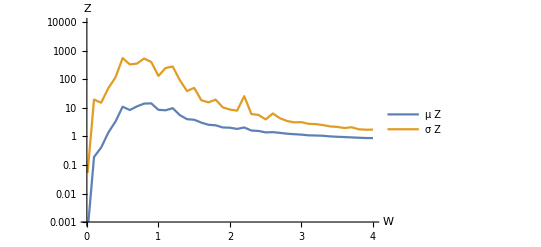

```mathematica
ListLogPlot[data,PlotLegends->{"μ Z","σ Z"},PlotRange->{{0,4},{0.001,10000}},AxesLabel->{W,Z},Joined->True]
```

To try to make sense of this, we simply further by removing the input fluctuations.   Here are our empirical findings:
For #W=0, #Z quickly reaches 0 and stays there.
For #W=1, if #Z is initially 0, it stays there; but when #Z starts at 1 or higher, the simulation occasionally returns #Z to 0 but usually simply hangs.
For #W=2 and higher, #Z fluctuates a lot, but seldom exceeds 40 even in very long simulations.

```mathematica
CRNrestore[W,Z]
```

{2 W →^1 2 W+Z ,2 W+Z →^2 2 W ,Z →^1 0 ,W+Z →^2 W+2 Z }

```mathematica
tmax=10000; vol=1;rsys=RescaleVolume[CRNrestore[W,Z]~Join~{conc[W,2],conc[Z,0]},vol];
trajectory=SimulateRxnsysSSA[rsys,tmax];
ListLinePlot[PlotFormat[trajectory,1000],PlotRange->{{0,tmax},{0,All}},PlotLegends->SpeciesInRxnsys[rsys]]
```

Can we explain this behavior in terms of the Chemical Master Equation, i.e. by considering the state space for Z with transition rates depending on reaction propensities?  Yes, we can!  (And did, in a 2021 lecture.)  Whereas for #W=0 and for #W≥2, with every step large #Z counts are more likely to shrink than to grow, when #W=1 and #Z≥1:
	the transition rate from #Z to #Z+1 is (#W)(#W-1)+2(#W #Z) = 2 #Z, while
	the transition rate from #Z to #Z-1 is 2(#W)(#W-1)(#Z)+(#Z) = #Z,
so each step has a 2/3 chance of increasing #Z and a 1/3 chance of decreasing it.  #Z is likely to grow without bound rather than hitting 0.

### Stabilizing a target concentration or a target count

Does this mean that chemical computation with very low counts is futile?  No, we just need to learn how to design CRNs that are well-behaved at low counts.   It will be instructive to examine two CRNs that, in the standard volume V_0=1.66 fL, both adopt a steady-state distribution with mean count at or near 1.0.  We’ll start with the simple Poisson production / degradation circuit, and examine it in bulk and in four finite volumes.  In bulk or in any finite volume this CRN converges on a mean concentration of 1 nM, which corresponds to counts that scale linearly with the volume.

{1 →^1 X ,X →^1 0 }

mean levels: 1. nM, 99.2538±12.1502, 10.9435±3.51033, 0.991378±0.988554, 0.153432±0.376727.

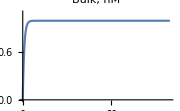
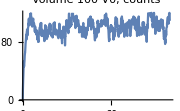
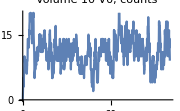
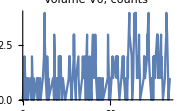
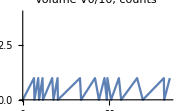

```mathematica
tmax=100;rsys=CRNconst[X,1];Print[rsys];
sol=SimulateRxnsys[rsys,tmax];
trajectory100=SimulateRxnsysSSA[RescaleVolume[rsys,100],tmax];
trajectory10=SimulateRxnsysSSA[RescaleVolume[rsys,10],tmax];
trajectory1=SimulateRxnsysSSA[RescaleVolume[rsys,1],tmax];
trajectory01=SimulateRxnsysSSA[RescaleVolume[rsys,0.1],tmax];
Print["mean levels: ",X[tmax]/.sol," nM, ",
Mean[WeightedTrajectory[trajectory100,1]],"±",StandardDeviation[WeightedTrajectory[trajectory100,1]],", ",
Mean[WeightedTrajectory[trajectory10,1]],"±",StandardDeviation[WeightedTrajectory[trajectory10,1]],", ",
Mean[WeightedTrajectory[trajectory1,1]],"±",StandardDeviation[WeightedTrajectory[trajectory1,1]],", ",
Mean[WeightedTrajectory[trajectory01,1]],"±",StandardDeviation[WeightedTrajectory[trajectory01,1]],". "];
{
Plot[X[t]/.sol,{t,0,tmax},PlotRange->{0,1.1},PlotLabel->"Bulk, nM",ImageSize->Small],
ListLinePlot[PlotFormat[trajectory100,1000],PlotRange->{0,120},PlotLabel->"Volume 100 V0, counts",ImageSize->Small],
ListLinePlot[PlotFormat[trajectory10,1000],PlotRange->{0,20},PlotLabel->"Volume 10 V0, counts",ImageSize->Small],
ListLinePlot[PlotFormat[trajectory1,1000],PlotRange->{0,4},PlotLabel->"Volume V0, counts",ImageSize->Small],
ListLinePlot[PlotFormat[trajectory01,1000],PlotRange->{0,4},PlotLabel->"Volume V0/10, counts",ImageSize->Small]
}
```

(How to interpret these plots:  Recall that (a) the trajectories are being subsampled by PlotFormat, so not every state is plotted, and (b) ListLinePlot draws a straight line from state to state, while the CRN actually makes discrete instantaneous changes whenever a reaction occurs, so e.g. the count doesn’t gradually change from 0 to 1.  In the rightmost plot, the state is almost always 0, occasionally popping up to 1 and typically then right back down to 0 again.)

The second CRN also has two reactions, the first of which is the same (spontaneously produce X with rate constant 1) while the second is the autocatalytic degradation reaction 2 X → X, with a high reaction rate constant of 1000.   In our reference volume V_0, this CRN maintains a count of exactly 1 with very little variance; it only rarely pops up to 2 for an instant; exceedingly rarely reaching 3 or more.   This remains true for all smaller volumes, as well as for slightly larger volumes; however as the volume approaches bulk, the steady-state concentration approaches √(1/1000).   That is to say, above a threshold volume, the mean count scales linearly with volume, but below that volume, the mean count is just 1, with less and less variance.

{1 →^1 X ,2 X →^1000 X }

mean levels: 0.0316228 nM, 3.42495±1.24339, 1.04919±0.225566, 0.985927±0.12361, 0.990529±0.105003.

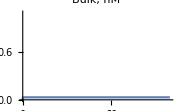
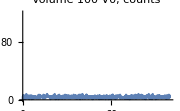
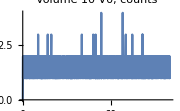
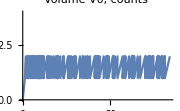
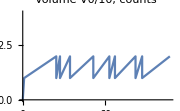

```mathematica
tmax=100;rsys={rxn[0,X,1],rxn[2X,X,1000]};Print[rsys];
sol=SimulateRxnsys[rsys,tmax];
trajectory100=SimulateRxnsysSSA[RescaleVolume[rsys,100],tmax];
trajectory10=SimulateRxnsysSSA[RescaleVolume[rsys,10],tmax];
trajectory1=SimulateRxnsysSSA[RescaleVolume[rsys,1],tmax];
trajectory01=SimulateRxnsysSSA[RescaleVolume[rsys,0.1],tmax];
Print["mean levels: ",X[tmax]/.sol," nM, ",
Mean[WeightedTrajectory[trajectory100,1]],"±",StandardDeviation[WeightedTrajectory[trajectory100,1]],", ",
Mean[WeightedTrajectory[trajectory10,1]],"±",StandardDeviation[WeightedTrajectory[trajectory10,1]],", ",
Mean[WeightedTrajectory[trajectory1,1]],"±",StandardDeviation[WeightedTrajectory[trajectory1,1]],", ",
Mean[WeightedTrajectory[trajectory01,1]],"±",StandardDeviation[WeightedTrajectory[trajectory01,1]],". "];
{
Plot[X[t]/.sol,{t,0,tmax},PlotRange->{0,1.1},PlotLabel->"Bulk, nM",ImageSize->Small],
ListLinePlot[PlotFormat[trajectory100,1000],PlotRange->{0,120},PlotLabel->"Volume 100 V0, counts",ImageSize->Small],
ListLinePlot[PlotFormat[trajectory10,1000],PlotRange->{0,4},PlotLabel->"Volume 10 V0, counts",ImageSize->Small],
ListLinePlot[PlotFormat[trajectory1,1000],PlotRange->{0,4},PlotLabel->"Volume V0, counts",ImageSize->Small],
ListLinePlot[PlotFormat[trajectory01,1000],PlotRange->{0,4},PlotLabel->"Volume V0/10, counts",ImageSize->Small]
}
```

The broader point is that in stochastic CRNs at a particular volume, different circuits can have the same mean but very different noise characteristics, as well as very different scaling of the mean count with volume.

### Dual-rail stochastic digital circuits for single-copy use

Now let’s develop a digital circuit implementation that works well with small volumes where each wire’s signal is represented by a single copy of a molecule.  

We’ll use a dual-rail approach, wherein circuit wire X is represented by two species, X[0] and X[1], exactly one of which will be present in 1 copy at all times.  The idea is very simple:  a trimolecular reaction recognizes when the output of a gate disagrees with what it should be, and fixes it.  The same pattern of reactions can work for any two-input gate.

We illustrate with and AND gate. Also note that when building a larger circuit using these modules, the initial state of the output is being set by a conc[ ] statement, so the only thing left to do when running the circuit will be to add conc[ ] statements introducing the input molecules.  Note that the gate output molecules could have been set to a random state, e.g. Z[0] or Z[1], at the beginning of a simulation, and all would be OK.  We set them to Z[0] just for simplicity.

```mathematica
singlecopyGate[X_,Y_,Z_,f_]:=Flatten[Table[
rxn[X[Boole[x]]+Y[Boole[y]]+Z[Boole[!f[x,y]]],X[Boole[x]]+Y[Boole[y]]+Z[Boole[f[x,y]]],1],
{x,{False,True}},{y,{False,True}}]]~Join~{conc[Z[0],1]}
```

```mathematica
singlecopyGate[X,Y,Z,And]//Column
```

We don’t really need Identity gates or Not gates, because we could just incorporate negation into the upstream or downstream 2-input gate, if we allow for other lookup tables such as ANDNOT and ORNOT and so forth.  But we’ll do it this way because it’s simple and easy to understand.

```mathematica
singlecopyIdentity[W_,Z_]:={rxn[W[0]+Z[1],W[0]+Z[0],1],rxn[W[1]+Z[0],W[1]+Z[1],1], conc[Z[0],1]}
singlecopyNot[W_,Z_]:={rxn[W[0]+Z[0],W[0]+Z[1],1],rxn[W[1]+Z[1],W[1]+Z[0],1],conc[Z[0],1]}
```

```mathematica
singlecopyCircuit[circuit_]:=Flatten[circuit/.{
(z_->Not[x_]):>singlecopyNot[x,z],
(z_->(f_:(And|Nand|Or|Nor|Xor|Xnor))[x_,y_]):>singlecopyGate[x,y,z,f],
(z_->True):>conc[z[1],1],
(z_->False):>conc[z[0],1],
(z_->x_):>singlecopyIdentity[x,z] 
}]
```

To test it out, here is a simple circuit that computes the floor of the square root of a 4-bit integer, as a 2-bit output.

```mathematica
sqrtcircuit={Z1->Nor[X1,X2],Z2->Not[X4],Z3->And[X3,Z2],Z4->Or[Z1,Z3],Z5->And[Z1,X4],Z6->Nand[Z5,X3],Y1->Nand[Z6,Z4],Y2->Or[X3,X4]}
```

{Z1→X1⊽X2,Z2→!X4,Z3→X3&&Z2,Z4→Z1||Z3,Z5→Z1&&X4,Z6→Z5⊼X3,Y1→Z6⊼Z4,Y2→X3||X4}

```mathematica
TableForm[Flatten[Table[
{x4,x3,x2,x1}~Join~Boole[{Y2,Y1}/.EvaluateCircuit[sqrtcircuit,{X1->x1,X2->x2,X3->x3,X4->x4},{Y1,Y2}]],
{x4,{0,1}},{x3,{0,1}},{x2,{0,1}},{x1,{0,1}}],3],
TableHeadings->{None,{X4,X3,X2,X1,Y2,Y1}}]
```

```mathematica
rsys=singlecopyCircuit[sqrtcircuit]
```

```mathematica
trajectory=SimulateRxnsysSSA[Join[rsys,{conc[X4[1],1],conc[X3[0],1],conc[X2[1],1],conc[X1[1],1]}],10];
```

Rather than plotting binary counts as a function of time, with a different-colored line for each species, it is much easier to understand shown as a black/white array where each column represents a distinct species and each row represents a distinct time point (namely, one row for the initial state and for each state after each reaction event, so that the vertical axis represents time but not linearly). Here, black represents 1 / True, while white represents 0 / False.   Because I was lazy, you’ll have to scale the image just right to get the column labels to line up correctly.

```mathematica
ArrayPlot[trajectory["Values"],PlotLabel->SpeciesInRxnsys[rsys],ImageSize->Large]
```

Because this CRN will have no further reactions possible after the circuit is done computing, we can give it tmax=Infinity, and the simulation will return whenever it is done.
(This is slower than it really should be because the simulator spends its time re-compiling the CRN for each simulation; the simulation itself takes essentially no time.  If you aren’t using the C compiler, this is even faster than if you are!  The compilation is only really useful for long simulations.)

```mathematica
Flatten[Position[SpeciesInRxnsys[rsys],#]&/@{Y2[1],Y1[1]}]
```

```mathematica
TableForm[Flatten[Table[
trajectory=SimulateRxnsysSSA[Join[rsys,{conc[X4[x4],1],conc[X3[x3],1],conc[X2[x2],1],conc[X1[x1],1]}],Infinity];
{x4,x3,x2,x1}~Join~Last[trajectory["Values"]][[{12,10}]],
{x4,{0,1}},{x3,{0,1}},{x2,{0,1}},{x1,{0,1}}],3],
TableHeadings->{None,{X4,X3,X2,X1,Y2,Y1}}]
```

For completeness, let’s show that large circuits, such the ripple carry adder, also compute correctly every time.  

We will have to confront one technical issue.  In our Boolean circuits, we used some “subscripted” or “indexed” wire names, such as A[i], B[i], and S[i].   When converting to a dual-rail CRN, we similarly use indexing to convert wire W to species W[0] and W[1].  Thus, for wires that are already indexed, we would end up with CRN species such as A[i][0] and A[i][1].  While the CRN simulator works fine for singly-indexed species names, it cannot handle doubly-indexed species names.  (This may have been fixed in the most recent update of the simulator that we are using, but I haven’t tested it.)  Thus, we will need convert double indices such as A[i][0] into single compound indices such as A[i,0].

```mathematica
CompressSubscripts[rsys_]:=rsys/.{species_[arg1_][arg2_]:> species[arg1,arg2]}
```

```mathematica
rsys=CompressSubscripts[singlecopyCircuit[RippleCarryAdder[4]]]
```

```mathematica
StochAdderCRNTestSingleCopy[n1_,n2_]:=Module[{N=Length[IntegerDigits[Max[n1,n2],2]],bits1,bits2,circuit,inputwires,inputconcs,output,outputindices,rsys,trajectory},
bits1=IntegerDigits[n1,2,N];bits2=IntegerDigits[n2,2,N];
circuit=RippleCarryAdder[N];
Print["Boolean circuit has ",Length[circuit]," gates and ",Length[CircuitWires[circuit]]," wires."];
rsys=CompressSubscripts[singlecopyCircuit[circuit]]; 
Print["CRN contains ",Length[rsys]," reactions and ",Length[SpeciesInRxnsys[rsys]]," species and can add any two ",N," bit integers."];
inputwires=MapThread[Rule,{Table[A[i],{i,N-1,0,-1}],bits1}]~Join~MapThread[Rule,{Table[B[i],{i,N-1,0,-1}],bits2}];
inputconcs=inputwires/.{(s_[b_]->v_):>conc[s[b,v],1]};
trajectory=SimulateRxnsysSSA[Join[rsys,inputconcs],Infinity];
outputindices=Table[First[Flatten[Position[SpeciesInRxnsys[rsys],S[i,1]]]],{i,N,0,-1}];
Print[ArrayPlot[trajectory["Values"]]];
output=Table[Last[trajectory["Values"]][[i]],{i,outputindices}];
Print["The sum of ",n1," and ",n2," should be ",n1+n2,"."];
FromDigits[output,2]
]
```

Because the CRNs are large, these simulations also take most of their time compiling, alas, and are faster without the C compiler.  But it should be tolerable.

```mathematica
StochAdderCRNTestSingleCopy[17,68]
```

```mathematica
StochAdderCRNTestSingleCopy[RandomInteger[1000],RandomInteger[1000]]
```

```mathematica
StochAdderCRNTestSingleCopy[RandomInteger[10^6],RandomInteger[10^6]]
```

### Dual-rail stochastic digital circuits for low-copy use, and without reliable initial conditions (not covered in class -- just if you’re curious)

The single copy circuits above used relative few reactions (4 per gate) and were guaranteed to eventually stop with the correct output.   Perhaps it seems magical that despite the stochasticity and the low volume -- where our original Boolean circuit CRNs failed spectacularly! -- this new construction yields such perfect results with such little effort.

There is no magic.  Rather, we exploited a powerful assumption: that the initial state of the system has exactly one molecule for each wire.   Analogously, if we had presumed perfect 0 nM or perfect 1 nM inputs for our bulk CRN circuits, we would not have needed either restoration or digital abstraction, and our CRNs could have been much simpler.   That begs the question, what if, in the single-molecule scenario, the initial state cannot be guaranteed?   Initially, there may be too many molecules for a given wire, perhaps some representing different True/False choices, or perhaps there aren’t any at all.  We can use the circuit described a few sections above to enforce that each wire is represented by a single molecule, almost all the time.  For each wire X, we add:
	∅ →^s X[0]
	2 X[0] →^f X[0]
	2 X[1] →^f X[1]
	X[0] + X[1] →^(2f) X[0]
where s is a slow rate constant and f is a fast rate constant.   If there are initially more than one molecule present, they will quickly destroy each other until a single molecule is left.  (With n molecules, it will take roughly time O(1/f), since the slowest step is the last reaction when there are just 2 molecules left.) On the other hand, if there are initially no molecules for this wire, it will take expected time O(1/s) to get one.  

With one molecule of each input wire present (with the correct value), and one molecule of each gate wire present (with an arbitrary value), a circuit of depth D will correctly compute all N gates in expected time O(D ln N ), so long as no wire molecule creation events during that time.  There being N wires were an incorrect signal molecule could be created, we can say that if 1/(N s) >> (D  ln N ), the output is very likely to be correct most of the time -- specifically, ϵ=O(1)/(N s D ln N) is a decent upper bound on the fraction of time the output will be wrong.  That gives some guidance for how to set the rate constant s, based on the tolerated level of error.  

Interestingly, one can tolerate a larger creation rate s and hence faster approach to steady-state but also higher error rate using a few additional mechanisms for error-correction based on von Neumann’s “multiplexing” fault tolerance, which turn out to be closely related to the RESTORE gate with slightly larger volumes.  Understanding that rigorously is for another time.

Here, we will simply demonstrate by simulation that a new RESTORE gate work well enough with the single-molecule circuit design, but with the per-wire molecule count feedback adjusted to a chosen intermediate level.  In particular, since a gate updates in time roughly 1 if all wires have count 1, and updates in time roughly m/m^3 if the counts are m (there are m molecules to fix, and each reaction has propensity m^3), in order to make the creation timescale for regulating wire molecule counts to be such that errors are introduced only 1% of the time, we can choose rate constant s=m^2/100.  Then what should rate constant f be in order to achieve a steady-state mean count of m? The rate constants on the three degradation reactions were chosen such that the sum of their propensities is exactly f m (m-1) independent of how many of the m molecules are X[0] vs X[1].  So s=f m (m-1) ought to result balance production and degradation, and that should be about right.  (Trying this approach with m=1 perhaps is not a good idea.)

```mathematica
(* note that this RESTORE gate does nothing if the input W has count 1; to act, it relies on the input at least sometimes having a higher count *)
lowcopyRestore[W_,Z_]:={rxn[2W[0]+Z[1],2W[0]+Z[0],1],rxn[2W[1]+Z[0],2W[1]+Z[1],1],conc[Z[0],1]}
lowcopyNot[W_,Z_]:={rxn[2W[0]+Z[0],2W[0]+Z[1],1],rxn[2W[1]+Z[1],2W[1]+Z[0],1],conc[Z[0],1]}
```

```mathematica
regulateCount[rsys_,ks_,kf_]:=Flatten[rsys/.{conc[w_[b_],1]:>{rxn[0,w[0],ks],rxn[2w[0],w[0],kf],rxn[2w[1],w[1],kf],rxn[w[0]+w[1],w[0],2kf]}}]
```

```mathematica
lowcopyCircuit[circuit_,ks_,kf_]:=regulateCount[Flatten[circuit/.{
(z_->Not[x_]):>lowcopyNot[x,z],
(z_->(f_:(And|Nand|Or|Nor|Xor|Xnor))[x_,y_]):>Module[{W},singlecopyGate[x,y,W,f]~Join~lowcopyRestore[W,z]],
(z_->True):>conc[z[1],1],
(z_->False):>conc[z[0],1],
(z_->x_):>lowcopyRestore[x,z] 
}],ks,kf]
```

```mathematica
lowcopyInput[rsys_,ϵ_,ks_,kf_]:= Flatten[rsys/.{conc[w_[b_],1]:>{
rxn[0,w[b],(1-ϵ) ks],rxn[0,w[1-b],ϵ  ks],
rxn[2w[0],w[0],kf],rxn[2w[1],w[1],kf],rxn[w[0]+w[1],w[0],kf],rxn[w[0]+w[1],w[1],kf]
}}]
```

Warm up by trying it on a small circuit, the 4-bit square root.  It is interesting to see that while the total counts on each wire fluctuate considerably, their correctness fraction is fairly consistently quite high!

```mathematica
Clear[m,ks,kf];
rsys=Join[
lowcopyCircuit[sqrtcircuit,ks,kf],
lowcopyInput[{conc[X4[1],1],conc[X3[0],1],conc[X2[0],1],conc[X1[1],1]},0.01,ks,kf]
]/.{ks->m^2/100,kf->m/100/(m-1)}/.{m->10};
trajectory=SimulateRxnsysSSA[rsys,100];
```

```mathematica
rsys
```

```mathematica
ListLinePlot[PlotFormat[trajectory,1000],PlotRange->{0,All},PlotLegends->SpeciesInRxnsys[rsys]]
```

```mathematica
With[{sps={X1[1],X2[1],X3[1],X4[1]}},
ListLinePlot[PlotFormat[trajectory,rsys,sps,1000],PlotRange->{0,All},PlotLegends->sps]]
```

```mathematica
With[{sps={X1[0],X2[0],X3[0],X4[0]}},
ListLinePlot[PlotFormat[trajectory,rsys,sps,1000],PlotRange->{0,All},PlotLegends->sps]]
```

```mathematica
With[{sps={X1[1]+X1[0],X2[1]+X2[0],X3[1]+X3[0],X4[1]+X4[0]}},
ListLinePlot[PlotFormat[trajectory,rsys,sps,1000],PlotRange->{0,All},PlotLegends->sps]]
```

```mathematica
With[{sps={X1[1]/(X1[1]+X1[0]+0.01),X2[1]/(X2[1]+X2[0]+0.01),X3[1]/(X3[1]+X3[0]+0.01),X4[1]/(X4[1]+X4[0]+0.01)}},
ListLinePlot[PlotFormat[trajectory,rsys,sps,1000],PlotRange->{0,All},PlotLegends->sps]]
```

```mathematica
With[{sps=(#[1]/(#[1]+#[0]+0.01))&/@ {Z1,Z2,Z3,Z4,Z5,Z6}},
ListLinePlot[PlotFormat[trajectory,rsys,sps,1000],PlotRange->{0,All},PlotLegends->sps]]
```

```mathematica
With[{sps={Y1[1],Y2[1]}},
ListLinePlot[PlotFormat[trajectory,rsys,sps,1000],PlotRange->{0,All},PlotLegends->sps]]
```

```mathematica
With[{sps={Y1[1]/(Y1[1]+Y1[0]+0.01),Y2[1]/(Y2[1]+Y2[0]+0.01)}},
ListLinePlot[PlotFormat[trajectory,rsys,sps,1000],PlotRange->{0,All},PlotLegends->sps]]
```

```mathematica
Last/@PlotFormat[trajectory,rsys,{Y1[1]/(Y1[1]+Y1[0]+0.01),Y2[1]/(Y2[1]+Y2[0]+0.01)},1000]
```

```mathematica
Mean[Take[#,-100]]&/@PlotFormat[trajectory,rsys,{Y1[1]/(Y1[1]+Y1[0]+0.01),Y2[1]/(Y2[1]+Y2[0]+0.01)},1000]
```

We can simulate all 16 input cases, and play with ϵ and m to see how well the circuit can function at what size. (Smaller m implies that the volume could be shrunk, consistent with some finite molecule size, and equivalent behavior obtained.)  Because we only have estimated the parameters to set the input sub-CRNs to achieve a given mean count and correctness, I have empirically tuned it to ϵ/4 while testing the outputs with respect to ϵ.  It seems that 10 molecules per wire is functioning well for us here.  As is 5.  With our parameters, things get shaky at m=3 and m=2.  Don’t try m=1 because our kf formula has a singularity there; perhaps one could work out better parameters.

```mathematica
TestLowCopySqrt[ϵ_,m_]:=Module[{table},
table=Flatten[Table[
rsys=Join[
lowcopyCircuit[sqrtcircuit,ks,kf],
lowcopyInput[{conc[X4[x4],1],conc[X3[x3],1],conc[X2[x2],1],conc[X1[x1],1]},ϵ/4,ks,kf]
]/.{ks->m^2/100,kf->m/100/(m-1)};
trajectory=SimulateRxnsysSSA[rsys,10000/m^2];
(Round[Last[Mean[Take[#,-200]]],0.01]&/@PlotFormat[trajectory,rsys,
(#[1]/(#[1]+#[0]+0.01))&/@{X4,X3,X2,X1,Y2,Y1},1000]),
{x4,{0,1}},{x3,{0,1}},{x2,{0,1}},{x1,{0,1}}],3];
Print[TableForm[table,TableHeadings->{None,{X4,X3,X2,X1,Y2,Y1}}]];
Print["Worst input deviation is ",Max[Min[#,1-#]&/@Flatten[table[[;;,{1,2,3,4}]]]]];
Print[If[AllTrue[Round[table],
((Boole[{Y2,Y1}]/.EvaluateCircuit[sqrtcircuit,{X4->#[[1]],X3->#[[2]],X2->#[[3]],X1->#[[4]]},{Y1,Y2}])=={#[[5]],#[[6]]})&],"All outputs are correct relative to 50% threshold.","Some output is incorrect relative to 50% threshold."]];
Print["Outputs ",
If[AllTrue[table,((#[[5]]<ϵ || #[[5]]>1-ϵ)&&(#[[6]]<ϵ || #[[6]]>1-ϵ))&],"satisfy","violate"],
" digital abstraction for ϵ=",ϵ,"."];
table
]
```

```mathematica
table10=TestLowCopySqrt[0.2,10];
```

X4 | X3 | X2 | X1 | Y2 | Y1
0.04 | 0.04 | 0.14 | 0.01 | 0.01 | 0.03
0. | 0.15 | 0.06 | 0.97 | 0.06 | 1.
0.16 | 0.02 | 0.92 | 0.09 | 0.09 | 1.
0.06 | 0.07 | 0.74 | 0.99 | 0.04 | 1.
0.13 | 0.99 | 0.05 | 0. | 1. | 0.
0.01 | 0.93 | 0.11 | 0.98 | 0.99 | 0.
0.13 | 0.92 | 1. | 0. | 0.98 | 0.01
0. | 0.95 | 0.94 | 1. | 0.99 | 0.
0.9 | 0.11 | 0. | 0.02 | 0.96 | 0.01
1. | 0. | 0.05 | 0.87 | 1. | 1.
0.76 | 0.09 | 0.93 | 0. | 0.91 | 0.99
0.91 | 0.03 | 0.94 | 0.88 | 0.96 | 1.
0.93 | 0.89 | 0. | 0. | 1. | 1.
0.97 | 0.95 | 0. | 0.96 | 1. | 0.99
0.89 | 0.91 | 0.88 | 0. | 1. | 0.97
0.98 | 0.87 | 1. | 0.91 | 1. | 1.

Worst input deviation is 0.26

All outputs are correct relative to 50% threshold.

Outputs satisfy digital abstraction for ϵ=0.2.

```mathematica
table5=TestLowCopySqrt[0.2,5];
```

X4 | X3 | X2 | X1 | Y2 | Y1
0.04 | 0. | 0.12 | 0.1 | 0. | 0.07
0. | 0.23 | 0. | 1. | 0.12 | 0.94
0.15 | 0. | 0.8 | 0. | 0.12 | 0.87
0. | 0.11 | 1. | 0.96 | 0.04 | 0.99
0. | 0.92 | 0. | 0.29 | 0.94 | 0.01
0.07 | 0.93 | 0.01 | 0.85 | 0.98 | 0.03
0.09 | 0.93 | 0.97 | 0.06 | 0.97 | 0.01
0. | 0.86 | 0.86 | 0.99 | 0.93 | 0.02
0.97 | 0.15 | 0.11 | 0. | 0.98 | 0.12
0.96 | 0. | 0. | 0.85 | 0.97 | 0.97
1. | 0.03 | 0.91 | 0.04 | 0.99 | 0.97
0.89 | 0.06 | 0.98 | 0.94 | 0.92 | 0.99
1. | 0.85 | 0.1 | 0. | 0.99 | 0.88
1. | 1. | 0.09 | 0.87 | 0.98 | 0.99
0.82 | 1. | 0.83 | 0. | 0.99 | 0.92
1. | 1. | 1. | 0.93 | 0.99 | 0.99

Worst input deviation is 0.29

All outputs are correct relative to 50% threshold.

Outputs satisfy digital abstraction for ϵ=0.2.

```mathematica
table3=TestLowCopySqrt[0.2,3];
```

X4 | X3 | X2 | X1 | Y2 | Y1
0.17 | 0. | 0.21 | 0. | 0.19 | 0.32
0.27 | 0.18 | 0.01 | 1. | 0.39 | 0.98
0.16 | 0.03 | 0.96 | 0.18 | 0.11 | 0.94
0. | 0.03 | 0.94 | 0.98 | 0.02 | 0.97
0.09 | 0.97 | 0. | 0.07 | 0.98 | 0.05
0.02 | 0.66 | 0. | 1. | 0.64 | 0.25
0. | 0.9 | 0.86 | 0.15 | 0.93 | 0.12
0.09 | 0.72 | 0.99 | 0.95 | 0.82 | 0.51
0.92 | 0.06 | 0.05 | 0.11 | 0.95 | 0.25
0.85 | 0. | 0.06 | 1. | 0.9 | 0.95
0.91 | 0. | 0.91 | 0.15 | 0.95 | 0.95
0.92 | 0.05 | 0.98 | 1. | 0.9 | 0.98
0.96 | 0.89 | 0.07 | 0.01 | 0.92 | 0.8
1. | 0.98 | 0.05 | 0.87 | 0.95 | 0.83
0.83 | 0.94 | 1. | 0. | 0.98 | 0.72
1. | 1. | 0.46 | 0.72 | 0.98 | 0.89

Worst input deviation is 0.46

Some output is incorrect relative to 50% threshold.

Outputs violate digital abstraction for ϵ=0.2.

```mathematica
table2=TestLowCopySqrt[0.2,2];
```

X4 | X3 | X2 | X1 | Y2 | Y1
0.29 | 0.07 | 0. | 0. | 0.28 | 0.09
0.09 | 0.18 | 0.08 | 0.99 | 0.14 | 0.93
0.05 | 0. | 0.98 | 0. | 0. | 0.83
0. | 0.04 | 0.99 | 0.94 | 0. | 0.71
0. | 0.99 | 0.03 | 0.11 | 0.81 | 0.17
0.09 | 0.89 | 0. | 0.89 | 0.78 | 0.31
0. | 0.99 | 0.99 | 0. | 0.86 | 0.53
0. | 0.99 | 0.99 | 0.99 | 0.57 | 0.69
0.63 | 0.01 | 0. | 0. | 0.53 | 0.29
0.9 | 0. | 0. | 0.97 | 0.62 | 0.89
0.96 | 0.08 | 0.99 | 0.02 | 0.88 | 0.87
0.99 | 0. | 0.61 | 0.91 | 0.76 | 0.85
0.95 | 0.98 | 0. | 0.01 | 0.94 | 0.72
0.98 | 0.99 | 0.11 | 0.93 | 0.84 | 0.78
0.99 | 0.99 | 0.97 | 0.06 | 0.78 | 0.83
0.99 | 0.99 | 0.78 | 0.88 | 0.84 | 0.74

Worst input deviation is 0.39

Some output is incorrect relative to 50% threshold.

Outputs violate digital abstraction for ϵ=0.2.

Although we have no guarantees, let’s go all the way and try to get the ripple carry adder to work.  Well, OK, it works on the small example... let’s not press our luck.

```mathematica
StochAdderCRNTestLowCopy[n1_,n2_,ϵ_,m_]:=(* not done yet *)Module[{N=Length[IntegerDigits[Max[n1,n2],2]],bits1,bits2,circuit,ks=m^2/100,kf=m/100/(m-1),inputwires,inputconcs,input,output,rsys,trajectory,tmax},
bits1=IntegerDigits[n1,2,N];bits2=IntegerDigits[n2,2,N];
circuit=RippleCarryAdder[N];
Print["Boolean circuit has ",Length[circuit]," gates and ",Length[CircuitWires[circuit]]," wires."];
rsys=lowcopyCircuit[circuit,ks,kf]; tmax=100N/m^2;
Print["CRN contains ",Length[rsys]," reactions and ",Length[SpeciesInRxnsys[rsys]]," species and can add any two ",N," bit integers."];
inputwires=MapThread[Rule,{Table[A[i],{i,N-1,0,-1}],bits1}]~Join~MapThread[Rule,{Table[B[i],{i,N-1,0,-1}],bits2}];
inputconcs=inputwires/.{(s_[b_]->v_):>conc[s[b][v],1]};
rsys=CompressSubscripts[Join[rsys,lowcopyInput[inputconcs,ϵ/4,ks,kf]]];
trajectory=SimulateRxnsysSSA[rsys,tmax];
Print[ArrayPlot[trajectory["Values"]]];
input=(Last[Mean[Take[#,-200]]]&/@PlotFormat[trajectory,rsys,(A[#,1]/(A[#,1]+A[#,0]+0.01))&/@Range[0,N-1],1000])
~Join~(Last[Mean[Take[#,-200]]]&/@PlotFormat[trajectory,rsys,(B[#,1]/(B[#,1]+B[#,0]+0.01))&/@Range[0,N-1],1000]);
output=(Last[Mean[Take[#,-200]]]&/@PlotFormat[trajectory,rsys,(S[#,1]/(S[#,1]+S[#,0]+0.01))&/@Range[N,0,-1],1000]);
Print["Inputs are off by at most ",Max[Min[#,1-#]&/@input]," and outputs are off by at most ",Max[Min[#,1-#]&/@output],"."];
Print["The sum of ",n1," and ",n2," should be ",n1+n2,"."];
FromDigits[Round[output],2]
]
```

```mathematica
StochAdderCRNTestLowCopy[17,68,0.1,10]
```

### Solving Circuit-SAT search problems with Stochastic Semantics

Stochasticity provides a natural way for a chemical reaction network to solve inverse problems that require search.  A canonical example is the Circuit-SAT problem:  given a feedforward digital circuit and a desired output, find inputs that make the output true.  For example, if the circuit takes as input two 100-bit binary numbers, performs multiplication and outputs a 200-bit binary number representing the product, then the inverse problem is “factor this 200-bit number”.  The Circuit-SAT problem is NP-complete.  

To build a stochastic CRN that solves the Circuit-SAT problem, we convert each gate in the circuit into a set of 12 reactions that detect when something is wrong, and change either input or output.  Additional reactions are added that force the output species (or input species, or intermediate species) to the desired values.  When all reactions in the CRN go extinct, i.e. no reaction can fire, then a solution has been found.  If the problem is not solvable, the CRN continues trying forever -- much like the conventional WalkSAT algorithm that it was inspired by.  (Note that as the circuit gets larger, the CRN below takes longer and longer to find a solution.  To be competitive with algorithms like WalkSAT, one needs to introduce an additional element to the construction:  when trying to resolve the conflict in a gate, bias toward flipping bits that make as few other gates inconsistent as possible.)

```mathematica
searchGate1[X_,Y_,f_]:=Flatten[Table[{
rxn[X[Boole[x]]+Y[Boole[!f[x]]],X[Boole[x]]+Y[Boole[f[x]]],1],
rxn[X[Boole[x]]+Y[Boole[!f[x]]],X[Boole[!x]]+Y[Boole[!f[x]]],1]},
{x,{False,True}}]]
searchGate2[X_,Y_,Z_,f_]:=Flatten[Table[{
rxn[X[Boole[x]]+Y[Boole[y]]+Z[Boole[!f[x,y]]],X[Boole[x]]+Y[Boole[y]]+Z[Boole[f[x,y]]],1],
rxn[X[Boole[x]]+Y[Boole[y]]+Z[Boole[!f[x,y]]],X[Boole[x]]+Y[Boole[!y]]+Z[Boole[!f[x,y]]],1],
rxn[X[Boole[x]]+Y[Boole[y]]+Z[Boole[!f[x,y]]],X[Boole[!x]]+Y[Boole[y]]+Z[Boole[!f[x,y]]],1]},
{x,{False,True}},{y,{False,True}}]]
clampingReaction[wire_->value_]:=rxn[wire[1-value],wire[value],1]
```

```mathematica
searchCircuit[circuit_]:=Flatten[circuit/.{
(z_->Not[x_]):>searchGate1[x,z,Not],
(z_->(f_:(And|Nand|Or|Nor|Xor|Xnor))[x_,y_]):>searchGate2[x,y,z,f],
(z_->(True|1)):>clampingReaction[z,1],
(z_->(False|0)):>clampingReaction[z,0],
(z_->x_):>searchGate1[x,z,Identity] 
}]
```

```mathematica
initialSearchState[circuit_]:=With[{wires=CircuitWires[circuit]},
MapThread[conc[#1[#2],1]&,{wires,RandomChoice[{0,1},Length[wires]]}]]
```

```mathematica
CRNSolveCircuit[circuit_,known_]:=Module[{rsys,trajectory},
rsys= Join[searchCircuit[circuit], clampingReaction/@known,initialSearchState[circuit]];
trajectory=SimulateRxnsysSSA[rsys,Infinity];
Print[ArrayPlot[trajectory["Values"]]];
Replace[#,{s_[b_]:>(s->b)}]&/@Pick[SpeciesInRxnsys[rsys],(#>0&)/@Last[trajectory["Values"]]]
]
```

We test it out on the 4-bit square-root circuit.  We can clamp the output and search for an input (the inverse problem) or we could clamp the input and search for the output (the forward problem) or we could even clamp some input and some output and search for a case that matches both constraints.  One could even clamp an intermediate wire.   There may be more than one answer, in which case the first one that is stumbled upon is reported.

```mathematica
sqrtcircuit={Z1->Nor[X1,X2],Z2->Not[X4],Z3->And[X3,Z2],Z4->Or[Z1,Z3],Z5->And[Z1,X4],Z6->Nand[Z5,X3],Y1->Nand[Z6,Z4],Y2->Or[X3,X4]}
```

```mathematica
TableForm[Flatten[Table[
{x4,x3,x2,x1}~Join~Boole[{Y2,Y1}/.EvaluateCircuit[sqrtcircuit,{X1->x1,X2->x2,X3->x3,X4->x4},{Y1,Y2}]],
{x4,{0,1}},{x3,{0,1}},{x2,{0,1}},{x1,{0,1}}],3],
TableHeadings->{None,{X4,X3,X2,X1,Y2,Y1}}]
```

X4 | X3 | X2 | X1 | Y2 | Y1
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 1 | 1
0 | 1 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 1 | 0
1 | 0 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 1 | 0
1 | 1 | 0 | 0 | 1 | 0
1 | 1 | 0 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1

```mathematica
CRNSolveCircuit[sqrtcircuit,{Y2->1,Y1->0}]
```

-Graphics-

{X1→0,X2→0,X3→0,X4→1,Y1→0,Y2→1,Z1→1,Z2→0,Z3→0,Z4→1,Z5→1,Z6→1}

```mathematica
CRNSolveCircuit[sqrtcircuit,{X4->0,X3->0,X2->1,X1->1}]
```

```mathematica
CRNSolveCircuit[sqrtcircuit,{Y1->0,X4->1}]
```

-Graphics-

{X1→0,X2→0,X3→0,X4→1,Y1→0,Y2→1,Z1→1,Z2→0,Z3→0,Z4→1,Z5→1,Z6→1}

In general, the circuit being solved needn’t even be a feedforward circuit.  The gates are just constraints, and the stochastic CRN performs constraint satisfaction.

### Some relevant references

Winfree, Erik. “Chemical reaction networks and stochastic local search.” In International Conference on DNA Computing and Molecular Programming, pp. 1-20. Springer, Cham, 2019.